```mathematica
(*Gives a slider for manipulation*)
Manipulate[Range[n], {n,1,5,1}]
```

```mathematica
Manipulate[Style["ABC",50,c],{c, {Red,Green,Blue}}]
```

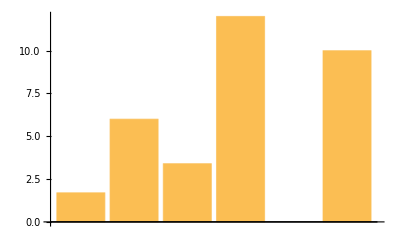

```mathematica
Manipulate[BarChart[{x,6,2x,12,3(7-x),10}], {x,1,6}]
```

```mathematica
(*We can even control the number of sides and color of a polygon*)
Manipulate[Graphics[Style[RegularPolygon[n], Hue[h]]], {n,5,20,1}, {h,0,1}]
```